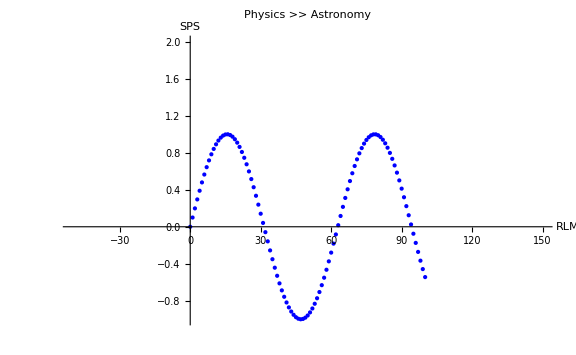

```mathematica
(*Problem 1*)
data =Table[{i,Sin[.1i]},{i,0,100}];
ListPlot[data,
PlotStyle->Blue,
PlotRange->{{-50,150},{-1,2}},AxesLabel->{Style["RLM",Blue,Medium,Bold],"SPS"},PlotLabel->Style["Physics >> Astronomy",Bold,Large,Orange],AxesStyle->Medium,
ImageSize->Large]
```

```mathematica
(*Problem 2*)
mat = Table[Table[Binomial[n,m],{m,0,9}],{n,0,9}];
Total[mat[[All,2]]]  (* n(n+1)/2 *)
Total[mat[[6,All]]] (*2^k*)
```

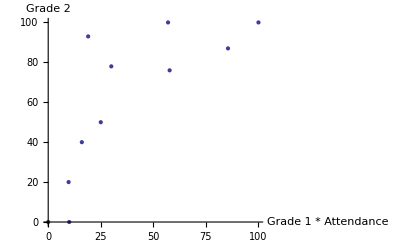

```mathematica
(*Problem 3*)
class={{"Name","Grade 1","Grade 2","Attendance"},
{"Michael",95,93,20},
{"George",95, 87, 90},
{"Oscar",50,78,60},
{"Lucille",100,0,10},
{"Lindsay",40,40,40},
{"Steve",0,0,100},
{"Barry",50,50,50},
{"Ron",100,100,57},
{"Rita",10,20,97},
{"Sally",100,100,100},
{"Maggie",77,76,75}};
ListPlot[Table[{class[[i,2]] * (class[[i,4]]/100),class[[i,3]]},{i,Length[table]}],PlotStyle->PointSize[Medium],
AxesLabel->{"Grade 1 * Attendance","Grade 2"}]
```